# Willem Nielsen Work

### DONE: Very Clean and General Perturbation function, Vis function, Analysis functions, Wfr for Pert function,visualize changes in cells and lifetimes. TODO: Different genes and phenotypes, Therapy search strategy

## Functions

### Utility

```mathematica
LocationDifferences[arr1_, arr2_, levelspec_:2] := Position[MapThread[{#1, #2} &, {arr1, arr2}, 2], {x_, y_} /; x != y, levelspec]
```

### Perturbation Viz

```mathematica
TrimArray[arr_,{width_,height_}]:=Module[
  {
    w,h,ranges,left,right,lt
  },
  w=If[
    width=!=None,
    ranges=DeleteCases[nonzeroRange /@ arr,{}];
    {left,right}={Min[ranges[[All,1]]],Max[ranges[[All,2]]]};
    #[[left-width ;; right+width]] & /@ arr,
    arr
  ];
  
  h=If[
    height=!=None,
    lt=Length[w]-LengthWhile[Reverse[w],Total[#]==0 &];
    w[[ ;; Min[lt+height,Length[w]]]],
    w
  ]
]
```

```mathematica
ClearAll@PlotCA
```

```mathematica
PlotCA[ca_, OptionsPattern[{ColorRules -> {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}, ArrayPlot}]] :=
 ArrayPlot[ca, ColorRules -> OptionValue[ColorRules], Mesh -> True, MeshStyle -> Opacity[0.1], ImageSize -> OptionValue[ImageSize]]
```

```mathematica
ClearAll@PlotDifferences
```

```mathematica
Options[PlotDifferences] = {"Trim" -> {1, 10}, ColorRules -> Join[{0 -> White, -100 -> GrayLevel[.9]}, 
    #1 :> Lighter[#2, .8] & @@@ {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    -#1 :> Darker[#2, .3] & @@@ {0->GrayLevel[1],1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]};
PlotDifferences[arr1_, arr2_, OptionsPattern[{PlotDifferences, ArrayPlot}]] := Module[{locs, vals, rus, highlighted, trimmed, colrules},
    locs = LocationDifferences[arr1, arr2];
    vals = arr2[[#1, #2]] & @@@ locs;
    rus = MapThread[#1 -> If[#2 == 0, -100, -#2] &, {locs, vals}];
    highlighted = ReplacePart[arr1, rus];
    trimmed = TrimArray[highlighted, OptionValue["Trim"]];
    ArrayPlot[trimmed, ColorRules -> OptionValue[ColorRules], MeshStyle -> Opacity[0.1], ImageSize -> OptionValue[ImageSize]]
    ]
```

```mathematica
ClearAll@HighlightPerturbations
```

```mathematica
Options[HighlightPerturbations] = {ColorRules->Join[{100->Black},
    #1 -> GrayLevel[0.9] & @@@ {1->Hue[0.06, 1, 1],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]},
    -#1 -> #2& @@@ {0->GrayLevel[1],1->RGBColor[1, 0, 0],2->Hue[0.73, 1, 1],3->Hue[0.14, 0.81, 0.99]}]};
HighlightPerturbations[ca_, ops:OptionsPattern[{HighlightPerturbations, PlotDifferences, ArrayPlot}]]:= Module[{},
locs = Position[ca, p[_]];
rus = ReplaceAll[#->-ca[[#[[1]], #[[2]], 1]]&/@ locs, 0:>100];
highlighted = ReplacePart[ca,rus];
trimmed = TrimArray[highlighted, OptionValue["Trim"]];
ArrayPlot[trimmed, ColorRules -> OptionValue[ColorRules], MeshStyle -> Opacity[0.1], ImageSize -> OptionValue[ImageSize]]
]
```

### Perturbation Function

```mathematica
nonzeroRange[list_] := 
Flatten[{FirstPosition[list, Except[0], Heads -> False], 1 + Length[list] - FirstPosition[Reverse[list], Except[0], Heads -> False]}]
```

```mathematica
towhite[k_, bit_] := {0}
tored[k_, bit_] := {1}
toblue[k_, bit_] := {2}
add1[k_, bit_] := If[bit == k - 1, {0}, {bit + 1}]
sub1[k_, bit_] := If[bit == 0, {k - 1}, {bit - 1}]
flipall[k_, bit_] := Complement[Range[0, k - 1], {bit}]
```

```mathematica
towhite[k_, bit_] := p[0]
tored[k_, bit_] := p[1]
toblue[k_, bit_] := p[2]
add1[k_, bit_] := If[bit == k - 1, p[0], p[bit + 1]]
sub1[k_, bit_] := If[bit == 0, p[k - 1], p[bit - 1]]
rand[k_, bit_] := p[RandomChoice[Complement[Range[0, k-1], {bit}]]]
```

```mathematica
sortfrom[list_, start_] :=
 Which[
  start == "Left", list,
  start == "Right", ReverseSort[list],
  start == "Center", SortBy[list, Abs[Median[list] - #] &],
  start == "Random", RandomSample[list, Length[list]],
  True, list
  ]
```

```mathematica
sortfrom[list_, start_] :=
 Which[
  start == "Left", list,
  start == "Right", ReverseSort[list],
  start == "Center", SortBy[list, Abs[Median[list] - #] &],
  start == "Random", RandomSample[list, Length[list]],
  True, list
  ]
```

```mathematica
getcolidxs[colidxs_, idxspec_]:= Replace[idxspec,
{
j_Integer:> sortfrom[colidxs, "Random"][[Select[Range[j], # <= Length[colidxs] &]]],
List[js__Integer]:> sortfrom[colidxs, "Random"][[Select[{js}, # <= Length[colidxs] &]]],
s_String:> sortfrom[colidxs, s][[{1}]],
List[s_String, jmax_Integer]:> sortfrom[colidxs, s][[Select[Range[jmax], # <= Length[colidxs] &]]],
List[s_String, List[js__Integer]]:>sortfrom[colidxs, s][[Select[{js}, # <= Length[colidxs] &]]],
List[s_String, List[List[jmin_Integer, jmax_Integer]]]:> sortfrom[colidxs, s][[Select[Range[jmin, jmax], # <= Length[colidxs] &]]]}
]
```

```mathematica
getidxs[idxs_, idxspec_]:= Replace[idxspec,
{j_Integer :>Select[{j}, # <= Length[idxs] &],
List[List[jmin_Integer, jmax_Integer]] :> Select[Range[jmin, jmax], # <= Length[idxs] &]}
]
```

```mathematica
PerturbCA[{ca_, rule_}, idxspec_:(10->1), pertbitfunc_:add1] := Module[{row, withall, colidxs, perturbedrowidxs, perturbedrow, perturbedCA},
row = ca[[idxspec[[1]]]];
withall = ReplaceAll[idxspec, All :> Range[Length[row]]];
colidxs = Replace[nonzeroRange[row], {{}:> {}, r_:> Range@@r}];
perturbedrowidxs = 
Replace[withall, 
  (*Color idx*)
  {Rule[i_, j_] :> getcolidxs[colidxs, j],
(*Row idx*) 
List[i_, j_] :> getidxs[Range[Length[row]],j]}];
perturbedrow = ReplacePart[row, #->pertbitfunc[rule[[2]], row[[#]]]&/@ perturbedrowidxs];perturbedCA = Sow[ReplacePart[ca, idxspec[[1]]->perturbedrow]];
       {perturbedCA, rule}
    ]
```

```mathematica
EvolvePerturbedCA[{pca_, rule_}]:= Module[{pidx, prowidx, pre, prow, evolvedCA},
pidx = FirstPosition[pca,p[_], {}];
If[pidx == {}, {pca, rule},
prowidx = pidx[[1]];
pre = pca[[;; prowidx- 1]];
prow =pca[[prowidx]]/.p[bit_]:>bit;
evolvedCA = Join[pre, CellularAutomaton[rule, prow, Length[pca] - Length[pre] - 1]];
    {evolvedCA, rule}
]]
```

```mathematica
PerturbedCAEvolution[rule_, init_, steps_:100, pertspec_ :"Random", pertbitfunc_:rand] := 
 Module[{ca = CellularAutomaton[rule, init, {steps, All}], cleanspec},
cleanspec =  
Replace[pertspec, 
{"Random" -> RandomInteger[{1, TestCALifeTime[ca]/.-Infinity:> steps}] -> 1,
i_Integer:> i -> 1}];
Replace[cleanspec,
{
Rule[_, _]:> EvolvePerturbedCA[Sow[PerturbCA[{ca, rule}, cleanspec, pertbitfunc]]][[1]],
 List[_Integer, _] :> EvolvePerturbedCA[Sow[PerturbCA[{ca, rule}, cleanspec, pertbitfunc]]][[1]],
List[__]:>   FoldList[EvolvePerturbedCA[Sow[PerturbCA[#1, #2]]]&, {ca, rule}, cleanspec][[All, 1]]
}]
     ]
```

### Analysis Functions

```mathematica
CountDifferences[arr1_, arr2_]:= Length[LocationDifferences[arr1, arr2]]
```

```mathematica
TestCALifeTime[ca_]:= If[#==0,-Infinity,Length[ca]-#+1]&[LengthWhile[Reverse[ca],Total[#]==0&]]
```

### PerturbedCAEvolution Options Syntax

```mathematica
row: {row->{"Random", {1}}}
row->jmax: {row->{"Random", Range[jmax]}}
row -> {j1, j2...}:  {row->{"Random", {j1, j2...}}}
row ->"Left": {row -> {"Left", 1}}
row ->{"Left", jmax}: {row->{"Left", Range[jmax]}}
{row->{"Order", {j1, j2...}}}
{10->1,15} : {10->1, 15->1}
{{10, 5}}: {{10, 5}}
{{10, {7, 8, 9, 10}}}
{10-> All}
{10, {{90, 100}}}
```

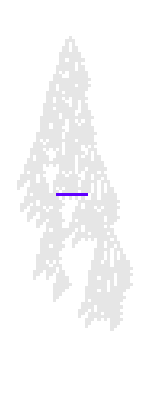

```mathematica
pca = Reap[PerturbCA[{initpat, ru}, 50->{"Center", {{1, 10}}}, toblue]][[2, 1, 1]];
HighlightPerturbations[pca]
```

#### SW Notes

```mathematica
{perspec,perbitfunc}
```

```mathematica
func[  {0,1,2,0,1,0,1,1,1,0}  ]
```

Pertbitfunc: 
“Random”
“SetValue” -> i
“AddValue” -> δ

Add value needs to be Mod

```mathematica
CellularAutomaton
```

```mathematica
extractKR[n_Integer]:={2,1}
```

```mathematica
extractKR[{_,k_Integer,r_Integer}]:={k,r}
```

#### WN Notes on Defining pertspec argument

```mathematica
x_-> {{{3, 5}},"Enumerate", pertbitfunc}
```

```mathematica
{{x_, y_}, pertbitfunc}
```

```mathematica
MarkPerturbations[{ca_, rule_}, pertspec_]
```

```mathematica
PerturbCA[]
```

```mathematica
PerturbCAEvolution[]
```

```mathematica
x_->
```

```mathematica
x_-> {pertbitfunc, rangespec}
```

```mathematica
{{{x_, y_}..}, pertbitfunc}
```

```mathematica
-1-> xxx
```

Challenge is how to integrate rangespec with a user inputed rangespec. No the range spec needs to happen before hand. The func can choose to select only white though which would be nice. pertbitfunc

It would be nice to have the pertbitfunc do the rangespec as well, but if the user doesn’t want to have to specify that right? Well let’s think about how to make that work.

So imagine the user puts in something like towhite. But then the challenge would be how to determine where to apply it. Well maybe you do the ranging afterwards? But what’s the point of that, why not just do it forwards. Yea true.

Okay so there’s no way around the ranging, it has to work that way.

## Running Code

### Init

```mathematica
CellularAutomaton[{6006804516645,3,1}, {{1}, 0}, {200, All}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

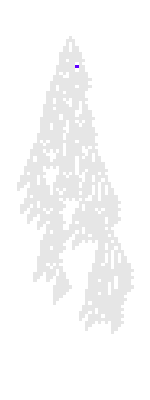

```mathematica
HighlightPerturbations[Reap[PerturbedCAEvolution[ru,init, steps, row]][[2, 1, 1]]]
```

```mathematica
PerturbCA[{CellularAutomaton[{6006804516645,3,1},{{1}, 0},{100,All}], {6006804516645,3,1}}, 10->1][[1, 10]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,p[0],2,1,1,2,1,0,1,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ru = {6006804516645,3,1};
initpat =CellularAutomaton[ru,{{1}, 0},{100,All}];
```

### Distribution of Disease Impacts

#### 30, Random, 1

```mathematica
SeedRandom[120529];
ecas = Table[PerturbedCAEvolution[ru, {{1}, 0},  100, 30->1][[2, 1]], 1000];
```

Change in countdiffs

```mathematica
cds = CountDifferences[initpat, #]&/@ ecas;
```

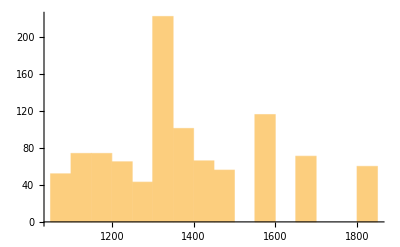

```mathematica
Histogram[cds, PlotRange->All]
```

#### Change in lifetime Random, Random, 1

```mathematica
SeedRandom[917623];
{eas, {pas}} = Reap[Table[PerturbedCAEvolution[ru, {{1}, 0},  200][[2, 1]], 1000]];
```

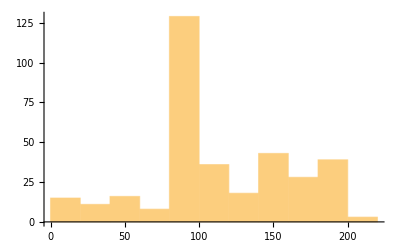

```mathematica
initlife = {{"[◼]", "TestLifetime"}}[ru];
newlts = TestCALifeTime/@ eas;
alive = DeleteCases[newlts, -Infinity];
Histogram[alive]
```

```mathematica
ResourceFunction["SelectPositions"][{1, 2, 3}, #>= 1&]
```

{{1},{2},{3}}

```mathematica
similar = Flatten[ResourceFunction["SelectPositions"][eas, TestCALifeTime[#]<95 && TestCALifeTime[#]>90&]];
Length[similar]
```

105

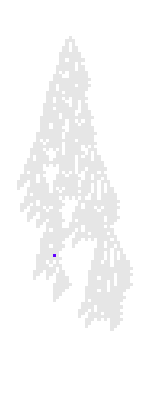
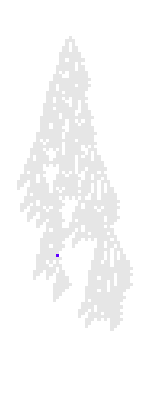
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
HighlightPerturbations[pas[[#]]]&/@ similar[[;;50]]
```

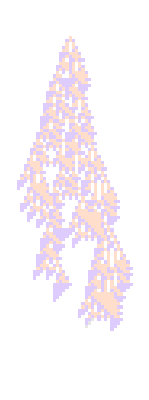
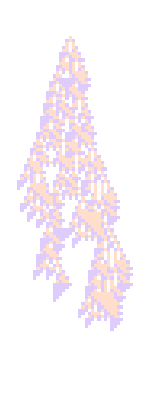
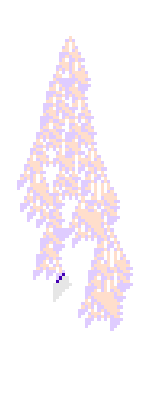
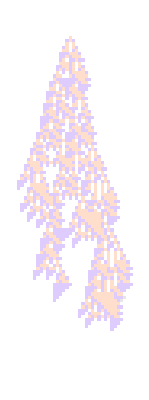
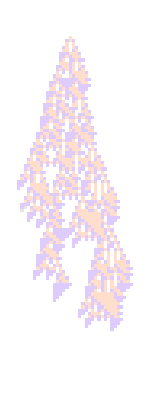
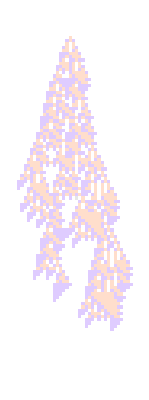
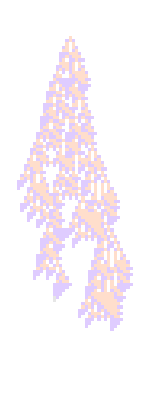
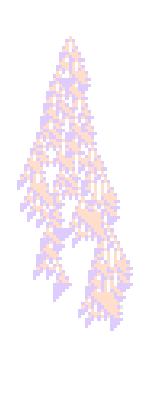
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotDifferences[initpat,# ]&/@ similar[[50;;70]]
```

#### Change in lifetime more runs

```mathematica
SeedRandom[1222];
ecas3 = Table[PerturbedCAEvolution[ru, {{1}, 0},  200][[2, 1]], 10000];
```

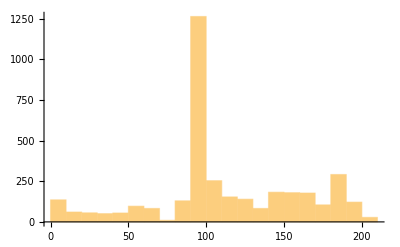

```mathematica
Histogram[DeleteCases[TestCALifeTime/@ ecas3, -Infinity]]
```

```mathematica
Length[DeleteCases[TestCALifeTime/@ ecas3, -Infinity]]
```

3663

### Distribution of Therapy Impacts

#### Initial disease

1438

-∞

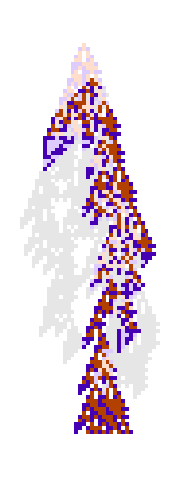

```mathematica
SeedRandom[1205];
pca = PerturbCA[{initpat, ru}, 10->1];
CountDifferences[initpat, pca[[1]]]
TestCALifeTime[pca[[1]]]
PlotDifferences[initpat, pca[[1]], ImageSize->Small]
```

#### Lifetime after treatment

Without deaths

```mathematica
SeedRandom[1111];
treated = Table[PerturbCA[pca, RandomInteger[{11 ,92}]-> 1], 10000];
evolved = EvolvePerturbedCA/@ treated;
(*HighlightPerturbations/@ treated[[;;10, 1]];*)
lts = TestCALifeTime/@ evolved[[All, 1]];
```

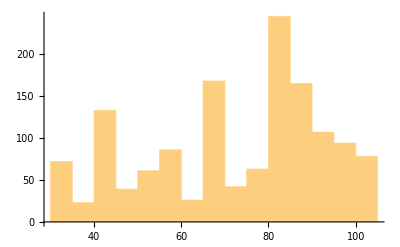

```mathematica
Histogram[lts]
```

With deaths

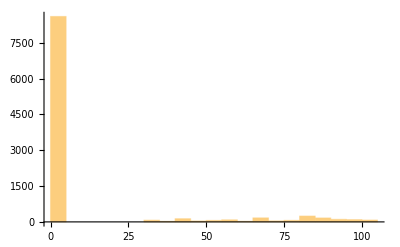

```mathematica
Histogram[Replace[lts, -Infinity->0, 1]]
```

#### Total Diffs

```mathematica
cds2 = CountDifferences[initpat, #]&/@evolved[[;;1000, 1]];
```

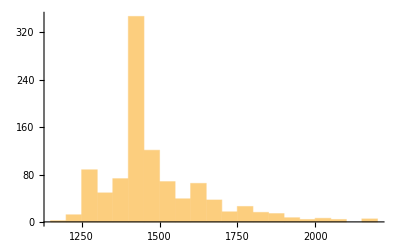

```mathematica
Histogram[cds2]
```

```mathematica
alive2 = Select[evolved, TestCALifeTime[#[[1]]]!= -Infinity&];
```

```mathematica
Length[alive2]
```

1382

```mathematica
cds3 = CountDifferences[initpat, #]&/@alive2[[All, 1]];
```

Only alive diffs

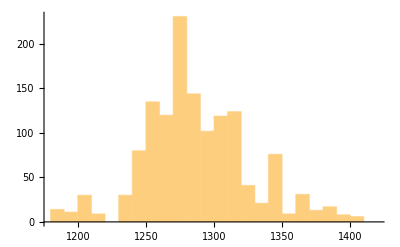

```mathematica
Histogram[cds3]
```

### Smaller Phenotype

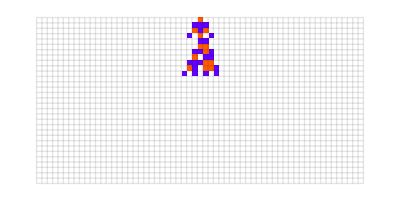

```mathematica
ru2 = {5586032021307, 3, 1};
initpat2 =CellularAutomaton[ru2,{{1}, 0},{30,All}];
PlotCA[initpat2]
```

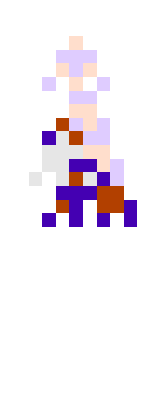
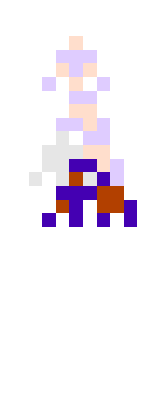
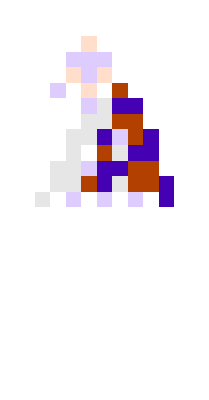
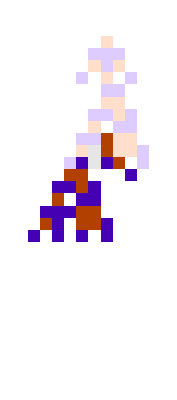
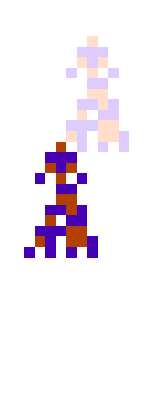
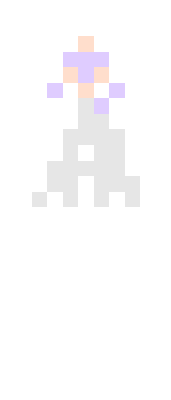
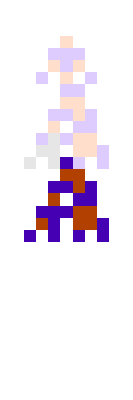
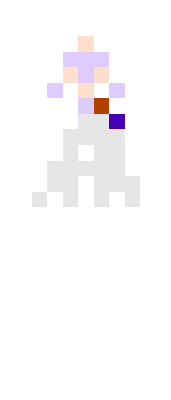
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[1125];
pcas = Table[PerturbedCAEvolution[ru2, {{1}, 0},30], 10];
PlotDifferences[initpat2, #]&/@ pcas
```

### Testing Final PerturbedCAEvolution

```mathematica
TestCALifeTime[initpat]
```

93

```mathematica
evo = PerturbedCAEvolution[ru, {{1}, 0}, 100, Table[i->1, {i, 10, 50}]]
```

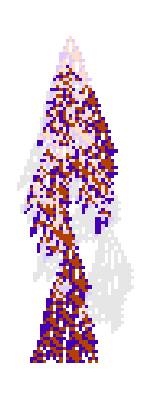
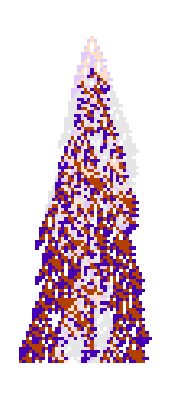
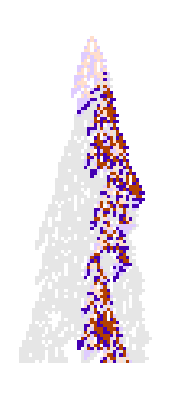
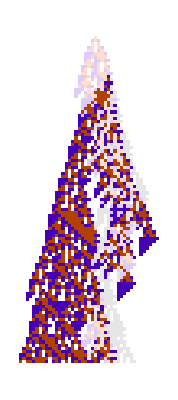
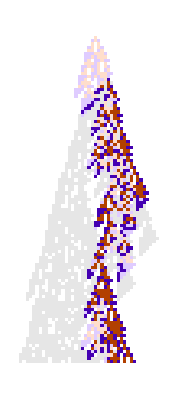
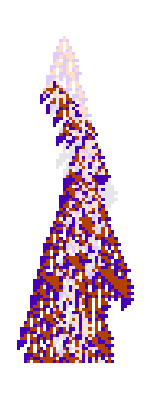
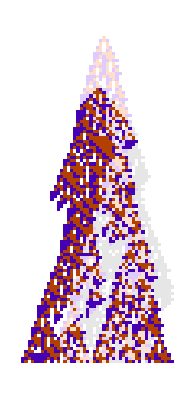
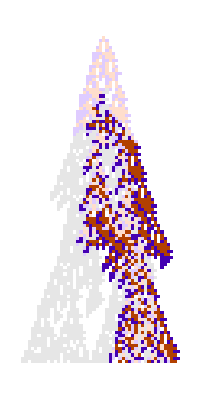
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotDifferences@@@Partition[evo, 2, 1]
```

### All diseases

```mathematica
alldis = Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Right"], {i,1, 92}, {j,1, 10}];
```

```mathematica
center =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Center"], {i,1, 92}, {j,1, 10}];
```

```mathematica
left =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left"], {i,1, 92}, {j,1, 10}];
```

```mathematica
white =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left", "PerturbationFunction"->towhite], {i,1, 92}, {j,1, 10}];
```

```mathematica
red =  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left", "PerturbationFunction"->tored], {i,1, 92}, {j,1, 10}];
```

```mathematica
blue=  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Left", "PerturbationFunction"->toblue], {i,1, 92}, {j,1, 10}];
```

```mathematica
all=  Table[PerturbeRow[{initpat, ru},i->j, "PerturbationStart"->"Center", "PerturbationFunction"->flipall], {i,1, 92}, {j,1, 4}];
```

$Aborted

### Increasing Disease Age

#### add1 Right 1

```mathematica
colrules
```

Join[0→GrayLevel[1],-100→GrayLevel[0.9],{0:>Lighter[GrayLevel[1],0.8],1:>Lighter[Hue[0.06, 1, 1],0.8],2:>Lighter[Hue[0.73, 1, 1],0.8],3:>Lighter[Hue[0.14, 0.81, 0.99],0.8]},{0:>Darker[GrayLevel[1],0.8],-1:>Darker[Hue[0.06, 1, 1],0.8],-2:>Darker[Hue[0.73, 1, 1],0.8],-3:>Darker[Hue[0.14, 0.81, 0.99],0.8]}]

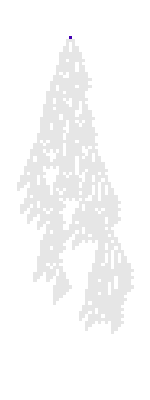
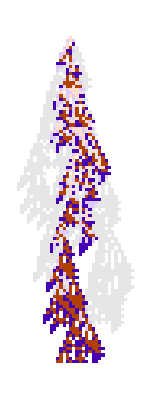
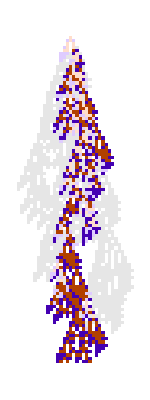
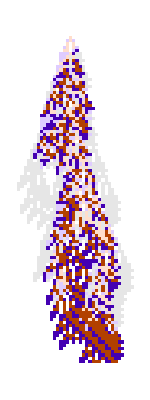
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowCADiffs[initpat, #, "Trim"->{1, None}]&/@  alldis[[;;5, 1, 1, 1]]
```

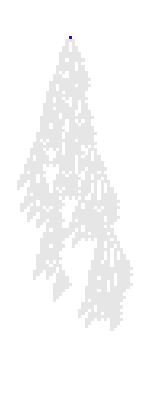
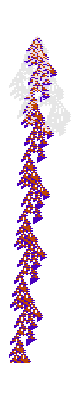
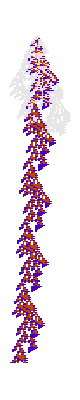
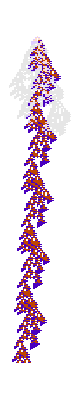
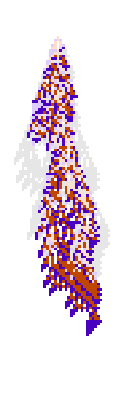
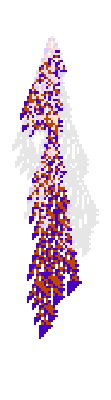
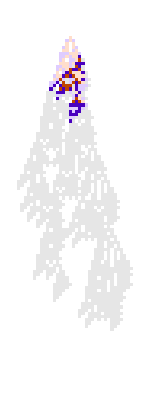
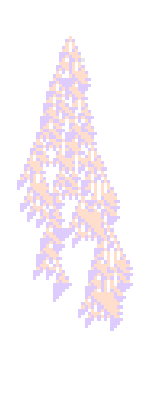
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[All, 1, 1, 1]]
```

#### add1 Right 5

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[All, 5, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Right 10

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[All, 10, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Center 1

```mathematica
ShowCADiffs[initpat, #]&/@  center[[All, 1, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Center 5

```mathematica
ShowCADiffs[initpat, #]&/@  center[[All, 5, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### add1 Center 10

```mathematica
ShowCADiffs[initpat, #]&/@  center[[All, 10, 1, 1]]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Symbol[]

#### add1 Left 1

```mathematica
ShowCADiffs[initpat, #]&/@  left[[All, 1, 1, 1]]
```

Integer[]

#### add1 Left 5

```mathematica
ShowCADiffs[initpat, #]&/@  left[[All, 5, 1, 1]]
```

Integer[]

#### add1 Left 10

```mathematica
ShowCADiffs[initpat, #]&/@  left[[All, 10, 1, 1]]
```

Integer[]

#### towhite Center 1

```mathematica
ShowCADiffs[initpat, #]&/@  white[[All, 1, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### towhite Center 5

```mathematica
ShowCADiffs[initpat, #]&/@  white[[All, 5, 1, 1]]
```

#### tored Center 1

```mathematica
ShowCADiffs[initpat, #]&/@  red[[All, 1, 1, 1]]
```

#### tored Center 5

```mathematica
ShowCADiffs[initpat, #]&/@  red[[All, 5, 1, 1]]
```

### Increasing Disease Intensity

```mathematica
Length/@alldis[[1, All, 1, 1]]
```

{301,301,301,301,301,301,301,301,301,301}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[10, All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[40, All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ShowCADiffs[initpat, #]&/@  alldis[[70, All, 1, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Single Round

```mathematica
ResourceFunction["FoldGraph"][f,{x},{a,b,c},VertexLabels->Automatic]
```

-Graphics-

```mathematica
PerturbeRow[{initpat}]
```

PerturbeRow[test]

```mathematica
ru = {6006804516645,3,1};
initpat =CellularAutomaton[ru,{{1}, 0},{100,All}];
(*p = PerturbeRows[{{initpat, initpat}, ru, {1}}, 10->1];
p2 = PerturbeRows[{p[[1]], ru, {2}}, 10->1];*)
```

```mathematica
p = PerturbedCAEvolution[ru, {{1}, 0}, 100, {10->1, 15->1}];
```

$Aborted

```mathematica
pp1 = PerturbePoint[{initpat, ru}, {10, 1}, "PerturbationFunction"->]
```

add1

```mathematica
pp2 = PerturbePoint[pp1[[1]],{15,1}]
```

add1

```mathematica
pp = ResourceFunction["FoldGraph"][PerturbePoint[#1,#2, "PerturbationFunction"->flipall]&, {{initpat, ru}}, {{10, 1}, {15, 1}}]
```

flipall

flipall

flipall

-Graphics-

```mathematica
pp = ResourceFunction["FoldGraph"][PerturbeRow[#1,#2, "PerturbationFunction"->flipall]&, {{initpat, ru}}, {10->2, 15-> 2}]
```

-Graphics-

```mathematica
HighlightGraph[pp, VertexList[pp][[7]]]
```

-Graphics-

```mathematica
ShowCADiffs@@@Partition[VertexList[pp][[All, 1]], 2, 1]
```

{-Graphics-,-Graphics-}

```mathematica
Length[pp[[1]]]
```

2

```mathematica
ShowCADiffs[pp1[[1, 1]], pp2[[1, 1]]]
```

-Graphics-

```mathematica
Rest@ShowPerturbationEvolution[initpat, p]
```

{{{-Graphics-}},{{{-Graphics-}}}}

```mathematica
Replace[{10->1},x_Integer:>x->1,{1}]
```

{10→1}

```mathematica
Length[p[[2, 1, 1, 1]]]
```

101

```mathematica
Map[Length[#[[1]]]&, p]
```

{1,1}

```mathematica
Map[Length[#] &, p[[1, 1]], {1}]
```

{101}

```mathematica
getfirst[list_, level_]:= list[[#]]&@@Table[1, level]
```

```mathematica
getfirst[{{{1}}}, 1]
```

{{1}}

```mathematica
p[[#]]&@@Table[1, {1}[[1]]][[1]]
```

1

```mathematica
Map[ShowCADiffs[initpat,#] &, p[[2, 1]], {2}]
```

{{-Graphics-}}

```mathematica
ShowPerturbations[initpat, p[[2]], {2}]
```

{{-Graphics-}}

```mathematica
Map[ShowCADiffs[initpat, #]&, p2[[1]], {3}]
```

{{{-Graphics-}},{{-Graphics-}}}

```mathematica
Length[o[[1,2, 1]]]
```

101

```mathematica
Length[o[[1, 1]]]
```

1

```mathematica
p =PerturbeRow[pat,ru,10->1, "PerturbationStart"->"Center","PerturbationFunction"->flipall];
```

```mathematica
Options[ShowCADiffs]
```

{Trim→{1,10}}

2

```mathematica
plotca[pat]
```

-Graphics-

```mathematica
plotca@TrimCA[pat, {1, 10}]
```

-Graphics-

```mathematica
ShowCADiffs[pat, #]&@ p[[1]]
```

{}

{1,10}

-Graphics-

```mathematica
ArrayPlot[TrimCA[highlighted, {1, 10}], ColorRules->Join[#[[1]]*-1->#[[2]]&/@ customstyledata["Colors"], { -100->Black,_Integer->LightGray}]]
```

-Graphics-

#### All possible

```mathematica
ps = Table[PerturbePattern[{pat, ru},i->j, "PerturbationStart"->"Right", "Cut"->300, "PerturbationFunction"->towhite], {i,5, 10}, {j,1, 10}];
```

```mathematica
ps = Table[PerturbePattern[{pat, ru}, {10, i}, "PerturbationStart"->"Right", "Cut"->300, "PerturbationFunction"->add1], {i,1, 10}];
```

```mathematica
Map[showpatdiffs[pat, #, "Trim"->True]&,  ps[[ All, 1, 1]],{2}]
```

{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
t1_Integer : t1->1
```

```mathematica
10: 10->{1}
10->5: 10->{1, 2, 3, 4, 5}
10->{{5, 7}}: 10->{5, 6, 7}
10->{5, 6}: 10->{5, 6}
```

```mathematica
ReplaceAll[<|1->{{5,"Enumeration"}}|>, Rule[1,_]:>"h"]
```

<|1→{{5,Enumeration}}|>

```mathematica
assoc=<|"a"->1,"b"->2,"c"->3|>;
newAssoc=Replace[assoc,"b"->_:>("b"->42),{1}]
(*Output:<|"a"->1,"b"->42,"c"->3|>*)
```

<|a→1,b→2,c→3|>

## SW Notes

#### How to store results of perturbations

```mathematica
{1,2,0,1,p[0,1],XXXX}
```

```mathematica
p[_,1]->XXX
```

```mathematica
PerturbedCAEvolution[   ]
```

```mathematica
PerturbationIndicatorFunction->
```

```mathematica
p[0,1]
```

```mathematica
{0,1}
```

```mathematica
Apply[p]
```

```mathematica
Last
```

```mathematica
-#[[2]]&
```

```mathematica
<|0->XXX,1->2,2->0|>
```

#### How to specify perturbations

```mathematica
<|1->{{5,"Enumeration"}}|>
```

```mathematica
<|1->{{5,"Random"},{6,"Random"}}|>
```

```mathematica
<|1->{{5,f},{6,"Random"}}|>
```

```mathematica
5
```

```mathematica
{5,First}
```

```mathematica
Range[6]
```

{1,2,3,4,5,6}

```mathematica
Range[4,11]
```

{4,5,6,7,8,9,10,11}

```mathematica
First[ ]
```

```mathematica
Last[   ]
```

### Analysis functions

lifetime after perturbation   [ AKA fitness ]

number of cells that stay the same after perturbation

### ML for therapy

Fitness function is either (a) how many cells we can return to their original state, or (b) how close we can get the lifetime to the original